# Lab 10: LinearAlgebra -- Carter Colton

```mathematica
Clear["`*" ]
```

## Assignment 1: A Question of Ages

Alice is twice as old as Bob. Alice's age added to Bob's age is the same as Christa's age. Bob’s age added to Christa’s age is the same as David’s age. The sum of their four ages is 60. How old is each person?  
(a) Write down four equations based on these statements, where Alice's, Bob's, Christa's, and David’s ages are called a, b,  c, and d, respectively. 
(b) Put the equations in matrix form and solve LinearSolve command. You should obtain all four ages, which fit all of the given conditions!

a = 2b
a + b = c
b + c = d
a + b + c + d = 60

```mathematica
Mtest={{1,-2,0,0},{1,1,-1,0},{0,1,1,-1},{1,1,1,1}};
```

```mathematica
%//MatrixForm
```

(1 | -2 | 0 | 0
1 | 1 | -1 | 0
0 | 1 | 1 | -1
1 | 1 | 1 | 1)

```mathematica
solutions={0,0,0,60};
%//MatrixForm
```

(0
0
0
60)

```mathematica
answer=Dot[Inverse[Mtest], solutions];
answer //MatrixForm //N
```

(12.
6.
18.
24.)

```mathematica
LinearSolve[Mtest,solutions];
%//MatrixForm//N
```

(12.
6.
18.
24.)

## Assignment 2: Tr and Det Calculations

(a) Use Diagonal to extract the diagonal elements from the matrix M, and then Apply the Plus operation to obtain the sum of the diagonal elements. (The Total function would be easier, but I wanted you to see Apply. Its short cut is @@.)  Verify that this calculation agrees with Tr[M].
(b) Use Det to compute the determinant of M.  Then compute the determinant of M^-1 (meaning the inverse of M, which is not the Mathematica command M^-1).  How are the two determinants related?
(c) Create a 3x3 matrix whose determinant is 0. An easy way to do this is to force two of the column (or row) vectors that make up the matrix to be multiples of each other. Compute its determinant, then try to take the inverse.

```mathematica
M = {{1,2,3},{3,1,2},{2,3,1}};
%//MatrixForm
```

(1 | 2 | 3
3 | 1 | 2
2 | 3 | 1)

```mathematica
Diagonal[M]
```

{1,1,1}

```mathematica
Plus@@%
```

3

```mathematica
Tr[M]
```

3

```mathematica
Det[M]
```

18

```mathematica
Det[Inverse[M]]
```

1/18

The two determinants are reciprocals of each other

```mathematica
matrix={{1,2,3},{2,4,6},{4,6,8}};
%//MatrixForm
```

(1 | 2 | 3
2 | 4 | 6
4 | 6 | 8)

```mathematica
Det[matrix]
```

0

```mathematica
Inverse[matrix]
```

Inverse::sing: Matrix {{1,2,3},{2,4,6},{4,6,8}} is singular.

Inverse[{{1,2,3},{2,4,6},{4,6,8}}]

## Assignment 3: Coupled Harmonic Oscillators Part 1

For simplicity, let's set m = 1 and k_s=k_b=1 for some choice of units. Use Mathematica to solve the eigenvalue equation and determine what two frequencies are allowed, along with what the relationship is between u_0 and v_0 for each allowed frequency. Compare the two frequencies of the two modes to the frequency the masses would have if they were not coupled together. Qualitatively explain why the allowed frequencies are higher, lower, or the same as the uncoupled case.

By the way, notice how easily this approach could straight-forwardly be applied to a MUCH larger system of coupled masses and springs. You just have to be able to specify the appropriate “spring constant matrix”. In my Physics 581 class, I had students solve the problem for 100 masses and 101 springs, where there are 100 allowed frequencies. The answer to that problem turns out to be very closely connected to the allowed vibrational modes in a solid (you can think of the masses as being vibrating atoms and the springs as being the bonds between the atoms).

λ(u_0
v_0) = (k_b+k_s | -k_s
-k_s | k_b+k_s)(u_0
v_0)

```mathematica
uandv={u0,v0};
uandv//MatrixForm
```

(u0
v0)

```mathematica
kb=1;
ks=1;
m=1;
```

```mathematica
kmatrix={{kb+ks,-ks},{-ks,kb+ks}};
%//MatrixForm
```

(2 | -1
-1 | 2)

```mathematica
rightside=kmatrix.uandv;
rightside//MatrixForm
```

(2 u0-v0
-u0+2 v0)

```mathematica
Eigenvectors[kmatrix]
%//MatrixForm
```

{{-1,1},{1,1}}

(-1 | 1
1 | 1)

```mathematica
Eigenvalues[kmatrix]
```

{3,1}

lamda = m * omega^2
Two allowed values for the frequency are Sqrt[3] and 1

```mathematica
Eigensystem[kmatrix]
```

{{3,1},{{-1,1},{1,1}}}

The allowed frequency of Sqrt[3] has u0 at -1 and v0 at 1 while the eigenvector at 1 has u0 at 1 and v0 at 1

```mathematica
kb=5;
ks=1;
```

```mathematica
kmatrix2={{kb+ks,-ks},{-ks,kb+ks}};
%//MatrixForm
```

(6 | -1
-1 | 6)

```mathematica
Eigensystem[kmatrix]
```

{{3,1},{{-1,1},{1,1}}}

This shows that the two frequencies are the same as the coupled case. This is due to ω=√(λ/m). The eigenvalues do not change because the matrices are similar. Therefore, since the mass remains the same in the equation the allowed frequencies will not change regardless.

## Assignment 4: Coupled Harmonic Oscillators Part 2

Modify the code for the previous graph so that the springs match the situation for which you found the normal modes above (“strong coupling”). 
(a) Play around with the initial conditions and make plots of the displacement of the two masses for a few different initial conditions. Among other things, try the case where only one mass is given an initial displacement and neither has any initial velocity, as I just did for the weak coupling case above.
(b) Now give both masses initial displacements as in normal mode 1. Verify that the period you observe matches your predictions of the normal mode frequency from the last assignment. In case you’ve forgotten, period = 2π/ω. Change the time scale as appropriate. 
(c) Repeat, giving both masses initial displacements as in normal mode 2. 

No other set of initial conditions other than the ones you just tried will give rise to pure sinusoidal behavior (well, none with no initial velocity, anyway). Try it! And no purely sinusoidal behavior will exist at any other frequencies than the ones predicted by the normal modes. And the eigenvalues and eigenvectors are directly connected to the normal mode frequencies and patterns of oscillation.

```mathematica
Clear[m,kb,ks,u,v,M] (* in case these variables were set to values above *)
M = {{kb+ks,-ks},{-ks,kb+ks}};  (* the matrix of spring constants *)
unknowns ={u[t],v[t]};    (* This is the vector x, containing u(t) and v(t) *)
equations = (#==0&)/@ (m D[unknowns,{t,2}]+M.unknowns);
initialconditions = {u[0]==u0,u'[0]==uvel0,v[0]==v0,v'[0]==vvel0};  (* u0 and uvel0 are initial position and velocity for mass 1; v0 and vvel0 are same thing for mass 2 *)
positions = unknowns/.DSolve[{equations,initialconditions},unknowns,t][[1]];
```

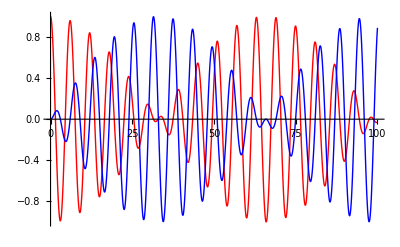

```mathematica
timedep = positions /.{m->1,kb->1,ks->0.1,u0->1, v0->0,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

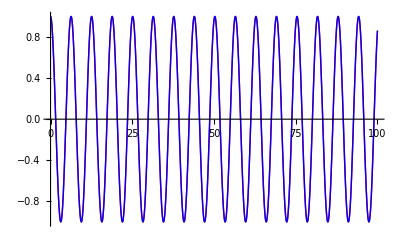

```mathematica
timedep = positions /.{m->1,kb->1,ks->1,u0->1, v0->1,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

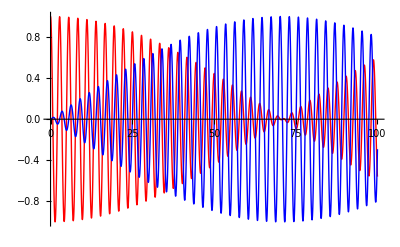

```mathematica
timedep = positions /.{m->1,kb->5,ks->0.1,u0->1, v0->0,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

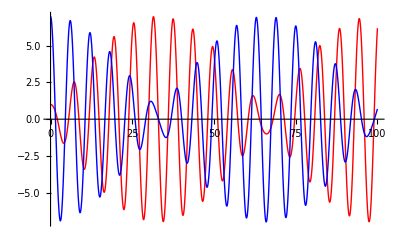

```mathematica
timedep = positions /.{m->1,kb->1,ks->0.1,u0->1, v0->7,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

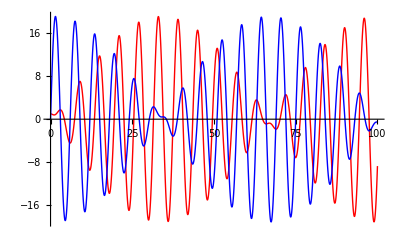

```mathematica
timedep = positions /.{m->1,kb->1,ks->0.1,u0->1, v0->0,uvel0->0,vvel0->20}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

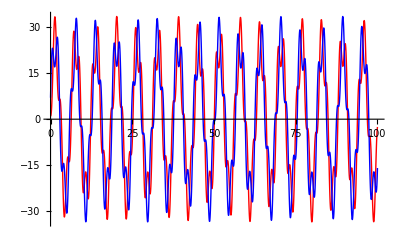

```mathematica
timedep = positions /.{m->1,kb->1,ks->5,u0->1, v0->7,uvel0->0,vvel0->50}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

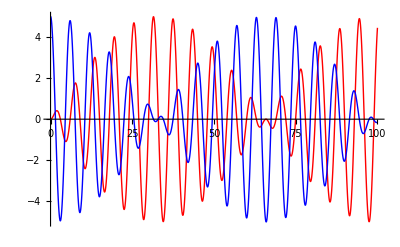

```mathematica
timedep = positions /.{m->1,kb->1,ks->0.1,u0->0, v0->5,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

```mathematica
timedep = positions /.{m->1,kb->1,ks->0.1,u0->1, v0->1,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

-Graphics-

```mathematica
N[2*Pi]
```

6.28319

That would be the period for the frequency of 1

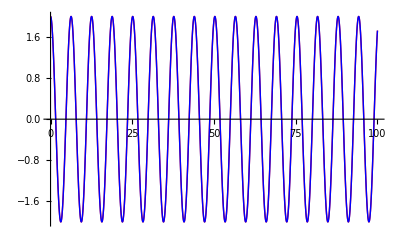

```mathematica
timedep = positions /.{m->1,kb->1,ks->0.1,u0->2, v0->2,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

```mathematica
N[2*Pi/Sqrt[3]]
```

3.6276

That would be the period for the frequency of the Sqrt[3]

## Assignment 5: 2D Rotation by an Angle

(a) Create a 2x1 column vector and call it v. It can be any vector you want. Calculate its length (via Norm). Then operate on your vector with the R2d matrix, using some angle between 30 and 90 deg. That is: vnew =  R2d . v.  Calculate the length of the resulting vector vnew... it should have the same length as the vector you started with!
(b) Use the Graphics and Arrow commands from Lab 3 to graphically view the vector rotation. Use the options Axes→True, AspectRatio→1, and use PlotRange to have the same scale on the x- and y-axes. You will likely need to use Flatten to get v and vnew into the right format for the Arrow command (look at the help page on Flatten to see what it does). Use different colors for your vectors.
(c) Verify that the angle (from the x-axis) for vnew compared to v has indeeed increased by the angle you chose. Use one of these two methods:  ArcTan with a pair of numbers, or Arg with a complex argument.
(d) Verify these properties of rotation matrices for a general two-dimensional rotation matrix (no angle specified): (1) det R = 1.  (2) inverse(R) = transpose(R). The Simplify command might be useful.

```mathematica
R2d = {{Cos[phi] , -Sin[phi]},{Sin[phi],Cos[phi]}};
% //MatrixForm
```

(Cos[phi] | -Sin[phi]
Sin[phi] | Cos[phi])

```mathematica
v={3,4};
v//MatrixForm
```

(3
4)

```mathematica
Norm[v]
```

5

```mathematica
vnew=R2d.v/.phi->45Degree
N[%]
```

{3/(√2)-2 √2,3/(√2)+2 √2}

{-0.707107,4.94975}

```mathematica
Norm[vnew]
N[%]
```

√((-3/(√2)+2 √2)^2+(3/(√2)+2 √2)^2)

5.

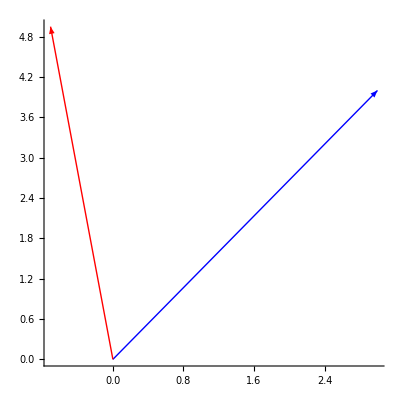

```mathematica
Graphics[{{Blue, Arrow[{{0,0},v}]},{Red,Arrow[{{0,0},vnew}]}},Axes->True,AspectRatio->1,PlotRange->Automatic]
```

```mathematica
anglev=N[Arg[v[[1]]+I*v[[2]]]/Degree]
```

53.1301

```mathematica
anglevnew=Arg[vnew[[1]]+I*vnew[[2]]]/Degree
N[%]
```

(π+ArcTan[(3/(√2)+2 √2)/(3/(√2)-2 √2)])/°

98.1301

```mathematica
anglevnew-anglev
```

45.

```mathematica
Det[R2d]
Simplify[%]
```

Cos[phi]^2+Sin[phi]^2

1

```mathematica
Simplify[Inverse[R2d]]
Simplify[Transpose[R2d]]
```

{{Cos[phi],Sin[phi]},{-Sin[phi],Cos[phi]}}

{{Cos[phi],Sin[phi]},{-Sin[phi],Cos[phi]}}

## Assignment 6: Some Matrix Invariants

```mathematica
M1 = {{7,2,3},{2,6,2},{3,2,1}} ;
```

(a) Construct a 3×3 matrix of random real numbers named S and use it to calculate the matrix M_2=S^-1 M_1 S, which will be similar to M_1 by definition. Hint: you can construct a matrix of random real numbers with a single RandomReal command, as I did above in the “Associative? Commutative?” section.
(b) Compute the traces of both M_1 and M_2. Are they equal?
(c) Compute the determinants of both M_1 and M_2. Are they equal?
(d) Compute the eigenvalues of both M_1 and M_2. Are they equal?
(e) Compute the eigenvectors of both M_1 and M_2. Are they equal? (The eigenvectors are the rows of the matrix returned by the Eigenvectors command.)

```mathematica
S=RandomReal[{-10,10},{3,3}];
%//MatrixForm
```

(-7.82621 | -9.47558 | -4.72852
-4.88523 | 7.29374 | -2.91655
-2.73365 | 0.652114 | -9.98094)

```mathematica
M2=Inverse[S].M1.S;
%//MatrixForm
```

(9.10289 | 0.185527 | 8.81709
-0.382678 | 4.32582 | -0.298684
1.08698 | 1.55305 | 0.571288)

```mathematica
Tr[M1]
Tr[M2]
```

14

14.

They are equal

```mathematica
Det[M1]
Det[M2]
```

-20

-20.

They are equal

```mathematica
N[Eigenvalues[M1]]
N[Eigenvalues[M2]]
```

{10.,4.44949,-0.44949}

{10.,4.44949,-0.44949}

They are equal

```mathematica
evM1=N[Eigenvectors[M1]]
evM2=N[Eigenvectors[M2]]
```

{{4.,3.,2.},{14.3485,-19.798,1.},{-0.348469,-0.202041,1.}}

{{-0.992105,0.0723032,-0.102464},{-0.451164,0.864922,0.219912},{0.678148,0.00837973,-0.734878}}

They are not equal

```mathematica
evM1//MatrixForm
evM2//MatrixForm
```

(4. | 3. | 2.
14.3485 | -19.798 | 1.
-0.348469 | -0.202041 | 1.)

(-0.992105 | 0.0723032 | -0.102464
-0.451164 | 0.864922 | 0.219912
0.678148 | 0.00837973 | -0.734878)

## Assignment 7: 2 Methods for Diagonalization

(a) Find the eigenvalues of the matrix M below and use them to produce a diagonal matrix which is similar to M.  No copying & pasting allowed. The command DiagonalMatrix will be helpful. (Note that the eigenvalues can be complex numbers.)
(b) Diagonalize M by defining the correct matrix S from the result of the Eigenvectors command (re-read the paragraph just above this assignment), and calculating S^-1.M.S. The result should match part (a). I found the Chop command to be helpful to remove the very small numbers that appeared in the off-diagonal elements due to internal rounding errors.
(c) Oddly enough, Mathematica does not have a built-in command to diagonalize a matrix. Let’s make one! Use Module to create a function called diagonalize, which takes a square numerical matrix as input and returns a diagonalized version of the matrix as output. Use either of the two methods from (a) or (b) as the guts for your Module. Test your function on the matrix M.

```mathematica
Clear[M]
```

```mathematica
M = RandomReal[{-10,10},{3,3}];
% //MatrixForm
```

(0.757346 | 6.27514 | 6.00295
-1.38208 | 9.51724 | -6.03875
-5.76811 | -2.41636 | -1.13415)

```mathematica
eM=Eigenvalues[M]
```

{11.2458+0. ⅈ,-1.05268+6.84324 ⅈ,-1.05268-6.84324 ⅈ}

```mathematica
dM=DiagonalMatrix[eM];
%//MatrixForm
```

(11.2458+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1.05268+6.84324 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -1.05268-6.84324 ⅈ)

```mathematica
evM=Eigenvectors[M];
%//MatrixForm
```

(-0.338537+0. ⅈ | -0.881284+0. ⅈ | 0.329745+0. ⅈ
0.75083+0. ⅈ | -0.123347+0.256162 ⅈ | -0.097453+0.588153 ⅈ
0.75083+0. ⅈ | -0.123347-0.256162 ⅈ | -0.097453-0.588153 ⅈ)

```mathematica
S=Transpose[evM];
%//MatrixForm
```

(-0.338537+0. ⅈ | 0.75083+0. ⅈ | 0.75083+0. ⅈ
-0.881284+0. ⅈ | -0.123347+0.256162 ⅈ | -0.123347-0.256162 ⅈ
0.329745+0. ⅈ | -0.097453+0.588153 ⅈ | -0.097453-0.588153 ⅈ)

```mathematica
newdiagonal=Inverse[S].M.S;
%//MatrixForm
```

(11.2458-4.93038×10^-32 ⅈ | -1.55431×10^-15+0. ⅈ | -1.11022×10^-15+0. ⅈ
2.22045×10^-16+4.21885×10^-15 ⅈ | -1.05268+6.84324 ⅈ | -7.77156×10^-16+0. ⅈ
8.88178×10^-16-4.66294×10^-15 ⅈ | -4.44089×10^-16+4.44089×10^-16 ⅈ | -1.05268-6.84324 ⅈ)

```mathematica
Chop[newdiagonal];
%//MatrixForm
```

(11.2458 | 0 | 0
0 | -1.05268+6.84324 ⅈ | 0
0 | 0 | -1.05268-6.84324 ⅈ)

```mathematica
diagonalizematrix[squarematrix_]:=Module[{},
esM=Eigenvalues[squarematrix];
dsM=DiagonalMatrix[esM]
]
```

```mathematica
diagonalizematrix[M];
%//MatrixForm
```

(11.2458+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1.05268+6.84324 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -1.05268-6.84324 ⅈ)

## Assignment 8: A Rotated Ellipse

(a) ContourPlot the ellipse, x^2+y^2/8=1.
(b) Rotate the ellipse 10° counter-clockwise, and plot the rotated ellipse.

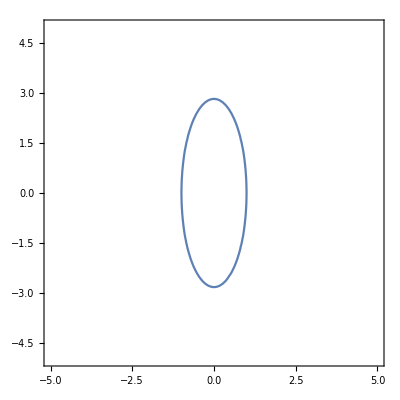

```mathematica
ContourPlot[x^2+y^2/8==1,{x,-5,5},{y,-5,5}]
```

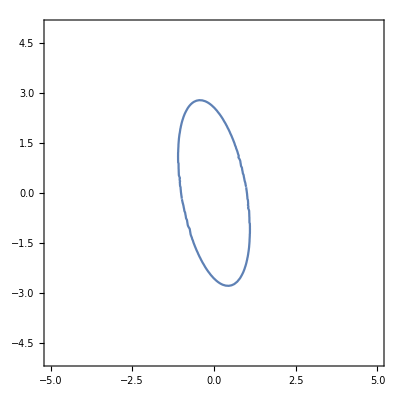

```mathematica
m = RotationMatrix[-10 Degree];  (* see below as to why this is -30 deg *)
{newx, newy} = m . {x,y};
newlhs = y /. y-> newy;
newrhs = Sqrt[8-8*x^2]  /. x-> newx;
newrhsneg=-Sqrt[8-8*x^2]  /. x-> newx;
plot1=ContourPlot[newlhs==newrhs, {x,-5,5},{y,-5,5}] ;
plot2=ContourPlot[newlhs==newrhsneg,{x,-5,5},{y,-5,5}];
Show[plot1,plot2]
```